# Quantum Mechanics

## Second Quantization

## Second Quantization

### Quantum Many-Body States

#### Identical Particles

Second quantization is a formalism used to describe quantum many-body systems of identical particles.

Classical mechanics: each particle is labeled by a distinct position r_i ⇒ any different configuration of {r_i} correspond to a different classical many-body state.

Quantum mechanics: particles are identical, such that exchanging two particles (r_i↔r_j) does not lead to a different quantum many-body state.

Permutation symmetry of identical particles ⇒ joint probability distribution must be invariant under permutation:

p(…,r_i,…,r_j,…)=p(…,r_j,…,r_i,…),

where the probability distribution p is related to the many-body wave function Ψ by

p(…,r_i,…,r_j,…)=(|Ψ(…,r_i,…,r_j,…)|)^2.

The wave function can only change up to an overall phase factor.

Ψ(…,r_i,…,r_j,…)=e^(ⅈ φ)Ψ(…,r_j,…,r_i,…).

It forms as a one-dimensional representation of the permutation group. Mathematical fact: there are only two 1-dim representations for any permutation group,

trivial representation ⇒ bosons

Ψ_B(…,r_i,…,r_j,…)=+Ψ_B(…,r_j,…,r_i,…)

sign representation ⇒ fermions

Ψ_F(…,r_i,…,r_j,…)=-Ψ_F(…,r_j,…,r_i,…)

#### Dirac Notations

Let us rephrase this using Dirac ket-state notation (more concise). Consider a complete set of single-particle states α (labeled by α)

α=∫ⅆ^d r ψ_α(r)r,

where ψ_α(r) is the wave function representing the state.

A two-particle state with the 1st particle in α_1 and the 2nd particle in α_2 will be described by

α_1⊗α_2=∫ⅆ^d r_1∫ⅆ^d r_2 ψ_α_1(r_1)ψ_α_2(r_2)r_1⊗r_2
=∫ⅆ^d r_1∫ⅆ^d r_2 Ψ(r_1,r_2)r_1⊗r_2.

Ψ(r_1,r_2)=ψ_α_1(r_1)ψ_α_2(r_2) is identified as the two-body wave function.

Exchanging r_1↔r_2 in the wave function Ψ(r_1,r_2) leads to a new wave function Ψ'(r_1,r_2)

Ψ'(r_1,r_2)=Ψ(r_2,r_1)=ψ_α_1(r_2)ψ_α_2(r_1)=ψ_α_2(r_1)ψ_α_1(r_2),

which corresponds to a new state

∫ⅆ^d r_1∫ⅆ^d r_2 Ψ'(r_1,r_2)r_1⊗r_2
=∫ⅆ^d r_1∫ⅆ^d r_2ψ_α_2(r_1)ψ_α_1(r_2)r_1⊗r_2
=α_2⊗α_1,

describing a two-particle state with the 1st particle in α_2 and the 2nd particle in α_1.

Conclusion: exchanging the positions of two particles (r_1↔r_2) ⇔ exchanging the labels of the single-particle state (α_1<->α_2).

#### First-Quantized States

First-quantization approach:

Suppose the single-particle Hilbert space is D dimensional, spanned by the single-particle basis states α (α=1,2,…,D).

The many-body Hilbert space of N particles will be D^N dimensional, spanned by the many-body basis states

[α]≡α_1⊗α_2⊗…⊗α_N,

where α_i=1,2,…,D labels the state of the ith particle.

A generic first-quantized state is a linear superposition of these basis states

Ψ=∑_[α] Ψ[α][α],

where the coefficient Ψ[α]∈ℂ is also called the many-body wave function (as a more general function of labels α_i not positions r_i).

Most of the first-quantized states are not qualified to describe systems of identical particles.

For identical bosons, Ψ[α] must be symmetric

Ψ_B(…,α_i,…,α_j,…)=+Ψ_B(…,α_j,…,α_i,…)

For identical fermions, Ψ[α] must be antisymmetric

Ψ_F(…,α_i,…,α_j,…)=-Ψ_F(…,α_j,…,α_i,…)

These states only span a subspace of the first-quantized Hilbert space.

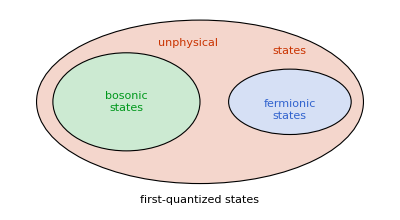

```mathematica
Graphics[{EdgeForm[Black],{Lighter[Red,0.8],Disk[{0,0},{2,1}],Red,Text["unphysical",{-0.15,0.72},{0,0},{1,0}],Text["states",{1.1,0.62},{0,0},{1,-0.25}]},{Lighter[Green,0.8],Disk[{-0.9,0},{0.9,0.6}],Green,Text[Style["bosonic\nstates",LineSpacing->{0.5,0}],{-0.9,0}]},{Lighter[Blue,0.8],Disk[{1.1,0},{0.75,0.4}],Blue,Text[Style["fermionic\nstates",LineSpacing->{0.5,0}],{1.1,-0.1}]},Text["first-quantized states",{0,-1.2}]}]
```

We would like to pick out (or construct) the basis states for the bosonic and fermionic subspaces. Starting from a generic basis state [α], we can construct

bosonic states by symmetrization

𝒮[α]=𝒮α_1⊗α_2⊗…⊗α_N
≡∑_(π∈S_N) α_(π(1))⊗α_(π(2))⊗…⊗α_(π(N)),

fermionic states by antisymmetrization

𝒜[α]=𝒜α_1⊗α_2⊗…⊗α_N
≡∑_(π∈S_N) (-)^π α_(π(1))⊗α_(π(2))⊗…⊗α_(π(N)),

π denotes an S_N group element and (-)^π is the permutation sign of π.

(-)^π=Piecewise[{{+1, if π has even number of inversions}, {-1, if π has odd number of inversions}}]

An inversion is a pair (x,y) such that x<y and π(x)>π(y). Take the S_3 group for example:

π(123) | 123 | 231 | 312 | 321 | 213 | 132
(-)^π | +1 | +1 | +1 | -1 | -1 | -1

Examples of bosonic states (unnormalized):

𝒮α⊗β=α⊗β+β⊗α, (assuming α≠β)
𝒮α⊗α=α⊗α.

Examples of fermionic states (unnormalized):

𝒜α⊗β=α⊗β-β⊗α, (assuming α≠β)
𝒜α⊗α=0 ⇒ no such fermionic state.

Pauli exclusion principle: two (or more) identical fermions can not occupy the same state simultaneously.

Originally α⊗β and β⊗α (for α≠β) are two orthogonal first-quantized states, under either symmetrization or antisymmetrization, they correspond to the same state (up to ±1 overall phase)

𝒮α⊗β=𝒮β⊗α,
𝒜α⊗β=-𝒜β⊗α.

The first-quantized Hilbert space is redundant ⇒ there are fewer basis states in the bosonic and fermionic subspaces.

Consider N particles, each can take one of D different single-particle states,

the dimension of bosonic subspace:

𝒟_B=((N+D-1)!)/(N!(D-1)!).

the dimension of fermionic subspace:

𝒟_F=(D!)/(N!(D-N)!).

It turns out that 𝒟_B+𝒟_F≤D^N as long as N>1 ⇒ the remaining basis states in the first-quantized Hilbert space are unphysical (for identical particles).

These unphysical states are annoying: we can not combine the states in the Hilbert space freely. We must always remember to symmetrized/antisymmetrized the state. ⇒ Is there a better way to organize the many-body Hilbert space, such that all states in the space are physical?

#### Second-Quantized States (Fock States)

Sometimes difficulties in physics arise from the inappropriate language we used. There are two different ways to describe many-body states:

In first-quantization, we ask: Which particle is in which state?

In second-quantization, we ask: How many particles are there in every state?

The question we ask in first-quantization is inappropriate: if the particles are identical, it will be impossible to tell which particle is which in the first place. We need to switch to a new language

```mathematica
Style[Grid[{{"\!\(|α⟩⊗|β⟩\)","","\!\(|β⟩⊗|α⟩\)"},{"the 1st particle on \!\(|α⟩\)\nthe 2nd particle in \!\(|β⟩\)"," ","the 1st particle on \!\(|β⟩\)\nthe 2nd particle in \!\(|α⟩\)"},{"↘"," ","↙"},{"there is one particle in \!\(|α⟩\), another particle in \!\(|β⟩\)",SpanFromLeft,SpanFromLeft}},Frame->{None,None,{{2,1}->True,{2,3}->True,{4,1}->True,{4,2}->True,{4,3}->True}},Alignment->{Center,Center}],14,LineSpacing->{0,14},FontFamily->"CMU"]
```

|α⟩⊗|β⟩ |  | |β⟩⊗|α⟩
the 1st particle on |α⟩
the 2nd particle in |β⟩ |   | the 1st particle on |β⟩
the 2nd particle in |α⟩
↘ |   | ↙
there is one particle in |α⟩, another particle in |β⟩ |  |

The new description does not require the labeling of particles. ⇒ It contains no redundant information. ⇒ It leads to a more precise and succinct description.

In the second-quantization approach,

Each basis state in the many-body Hilbert space is labeled by a set of occupation numbers n_α (for α=1,2,…,D)

[n]≡n_1,n_2,…,n_α,…,n_D,

meaning that there are n_α particles in the state α.

n_α=Piecewise[{{0,1,2,3,…, bosons,}, {0,1, fermions.}}]

For bosons, n_α can be any non-negative integer.

For fermions, n_α can only take 0 or 1, due to the Pauli exclusion principle.

The occupation numbers n_α sum up to the total number of particles, i.e. ∑_α n_α=N.

The states [n] are also known as Fock states.

All Fock states form a complete set of basis for the many-body Hilbert space, or the Fock space.

Any generic second-quantized many-body state is a linear combination of Fock states,

Ψ=∑_[n] Ψ[n][n].

#### Representation of Fock States

The first- and the second-quantization formalisms can both provide legitimate description of identical particles. (The first-quantization is just awkward to use, but it is still valid.)

Every Fock state has a first-quantized representation.

The Fock state with all occupation numbers to be zero is called the vacuum state, denoted as

0≡…,0,…

It corresponds to the tensor product unit in the first-quantization, which can be written as

0_B=0_F=1.

We use a subscript B/F to indicate whether the Fock state is bosonic (B) or fermionic (F). For vacuum state, there is no difference between them.

The Fock state with only one non-zero occupation number is a single-mode Fock state, denoted as

n_α=…,0,n_α,0,…

In terms of the first-quantized states

(1_α)_B=(1_α)_F=α,
(2_α)_B=α⊗α,
(3_α)_B=α⊗α⊗α,
n_α_B=(α⊗α⊗…⊗α)_(n_α factors)≡α^(⊗n_α).

For multi-mode Fock states (meaning more than one single-particle state α is involved), the first-quantized state will involve appropriate symmetrization depending on the particle statistics. For example,

(1_α,1_β)_B=1/(√2)(α⊗β+β⊗α),
(1_α,1_β)_F=1/(√2)(α⊗β-β⊗α).

Note the difference between bosonic and fermionic Fock states (even if their occupation numbers are the same). Here are more examples

(2_α,1_β)_B=1/(√3)(α⊗α⊗β+α⊗β⊗α+β⊗α⊗α),
(1_α,1_β,1_γ)_F=1/(√6)(α⊗β⊗γ+β⊗γ⊗α+γ⊗α⊗β-γ⊗β⊗α-β⊗α⊗γ-α⊗γ⊗β).

Ok, you get the idea. In general, the Fock state can be represented as

for bosons,

[n]_B=((∏_α n_α!)/(N!))^(1/2)𝒮 ⊗_α α^(⊗n_α).

for fermions,

[n]_F=1/(√(N!))𝒜 ⊗_α α^(⊗n_α).

𝒮 and 𝒜 are symmetrization and antisymmetrization operators defined in Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered).

### Creation and Annihilation Operators

#### State Insertion and Deletion

The creation and annihilation operators are introduced to create and annihilate particles in the quantum many-body system, as indicated by their names. The first step towards defining them is to understand how to insert and delete a single-particle state from the first-quantized state in a symmetric (or antisymmetric) manner.

Let us first declare some notations:

Let α, β be single-particle states.

Let 1 be the tensor identity (meaning that α⊗1=1⊗α=α).

Let Ψ, Φ be generic first-quantized states as in Eq. (DisplayFormulaNumbered).

Now we define the insertion operator ⊳_± and deletion operator ⊲_± by the following rules:

Linearity (for a,b∈ℂ)

α⊳_±(aΨ+bΦ)=aα⊳_±Ψ+bα⊳_±Φ,
α⊲_±(aΨ+bΦ)=aα⊲_±Ψ+bα⊲_±Φ.

Vacuum action

α⊳_±1=α,
α⊲_±1=0.

Recursive relation

α⊳_±β⊗Ψ=α⊗β⊗Ψ±β⊗(α⊳_±Ψ),
α⊲_±β⊗Ψ=αβΨ±β⊗(α⊲_±Ψ).

αβ=δ_αβ if α and β are orthonormal basis states. The subscript ± of the insertion or deletion operators indicates whether symmetrization (+) or antisymmetrization (-) is implemented.

#### Boson Creation and Annihilation

The boson creation operator b_α^† adds a boson to the single-particle state α, increasing the occupation number by one n_α→n_α+1. It acts on a N-particle first-quantized state Ψ as

b_α^†Ψ=1/(√(N+1))α⊳_+Ψ,

where α⊳_+ inserts the single-particle state α to N+1 possible insertion positions symmetrically.

The boson annihilation operator b_α removes a boson from the single-particle state α, reducing the occupation number by one n_α→n_α-1 (while n_α>0). It acts on a N-particle first-quantized state Ψ as

b_α Ψ=1/(√N)α⊲_+Ψ,

where α⊲_+ removes the single-particle state α from N possible deletion positions symmetrically.

##### Single-Mode Fock States

Based on these definitions, we can show that the creation and annihilation operators acting on single-mode Fock states as

b_α^†n_α=1/(√(n_α+1))α⊳_+α^(⊗n_α)
=(n_α+1)/(√(n_α+1))α^(⊗(n_α+1))
=√(n_α+1)n_α+1.

b_α n_α=1/(√n_α)α⊲_+α^(⊗n_α)
=n_α/(√n_α)α^(⊗(n_α-1))
=√n_α n_α-1.

Thus we conclude

b_α^†n_α=√(n_α+1)n_α+1,
b_α n_α=√n_α n_α-1.

Especially, when acting on the vacuum state

b_α^†0_α=1_α,
b_α 0_α=0.

Using Eq. (DisplayFormulaNumbered), we can show that

b_α^†b_α n_α=n_α n_α,

meaning that b_α^†b_α is the boson number operator of the α state.

All the single-mode Fock state can be constructed by the boson creation operator from the vacuum state

n_α=1/(√(n_α!))(b_α^†)^n_α 0_α.

##### Generic Fock States

The above result can be generalized to any Fock state of bosons

b_α^†(…,n_β,n_α,n_γ,…)_B=√(n_α+1)(…,n_β,n_α+1,n_γ,…)_B,
b_α(…,n_β,n_α,n_γ,…)_B=√n_α(…,n_β,n_α-1,n_γ,…)_B.

These two equations can be considered as the defining properties of boson creation and annihilation operators.

##### Operator Identities

Eq. (DisplayFormulaNumbered) implies the following operator identities

[b_α^†,b_β^†]=[b_α,b_β]=0, [b_α,b_β^†]=δ_αβ.

These relations can be considered as the algebraic definition of boson creation and annihilation operators.

#### Fermion Creation and Annihilation

The fermion creation operator c_α^† adds a fermion to the single-particle state α, increasing the occupation number by one n_α→n_α+1 (while n_α=0). It acts on a N-particle first-quantized state Ψ as

c_α^†Ψ=1/(√(N+1))α⊳_-Ψ,

where α⊳_- inserts the single-particle state α to N+1 possible insertion positions anti-symmetrically.

The fermion annihilation operator c_α removes a fermion from the single-particle state α, reducing the occupation number by one n_α→n_α-1 (while n_α=1). It acts on a N-particle first-quantized state Ψ as

c_α Ψ=1/(√N)α⊲_-Ψ,

where α⊲_- removes the single-particle state α from N possible deletion positions anti-symmetrically.

##### Single-Mode Fock States

Based on these definitions, we can show that the creation and annihilation operators acting on single-mode Fock states as

c_α^†0_α=α⊳_-1=α=1_α
c_α^†1_α=1/(√2)α⊳_-α=1/(√2)(α⊗α-α⊗α)=0

c_α 0_α=0
c_α 1_α=α⊲_-α=1=0_α.

Thus we conclude (note that n_α=0,1 only take two values)

c_α^†n_α=√(1-n_α)1-n_α,
c_α n_α=√n_α 1-n_α.

Using Eq. (DisplayFormulaNumbered), we can show that

c_α^†c_α n_α=n_α n_α,

meaning that c_α^†c_α is the fermion number operator of the α state.

All the single-mode Fock state can be constructed by the boson creation operator from the vacuum state

n_α=(c_α^†)^n_α 0_α.

##### Generic Fock States

The above result can be generalized to any Fock state of bosons

c_α^†(…,n_β,n_α,n_γ,…)_F=(-)^(∑_(β<α) n_β)√(1-n_α)(…,n_β,1-n_α,n_γ,…)_F,
c_α(…,n_β,n_α,n_γ,…)_F=(-)^(∑_(β<α) n_β)√n_α(…,n_β,1-n_α,n_γ,…)_F.

These two equations can be considered as the defining properties of fermion creation and annihilation operators.

##### Operator Identities

Eq. (DisplayFormulaNumbered) implies the following operator identities

{c_α^†,c_β^†}={c_α,c_β}=0, {c_α,c_β^†}=δ_αβ.

These relations can be considered as the algebraic definition of fermion creation and annihilation operators.